```mathematica
(* after running visio.nb run Init data, rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ], Error Estimation*)
```

### Init data

```mathematica
ρ0=1;
L1=Lx;
L2=Ly;
γ=1.4;
c=1;
eps=10^-3;
alphaa=1;
timeP = 3.0;
offset = 5;
initrho[r_]:=eps Exp[-alphaa (r-offset)^2]
F[r_]:=initrho[r]+ρ0
```

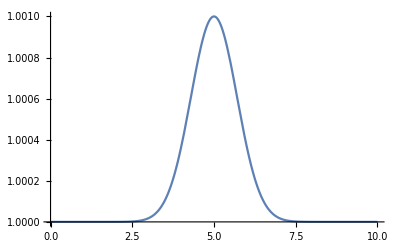

```mathematica
Plot[F[r],{r,0,Lx}]
```

### Analytical solutions for density, velocity, pressure, energy

```mathematica
rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(F[x-c t]+F[x+c t])/2
```

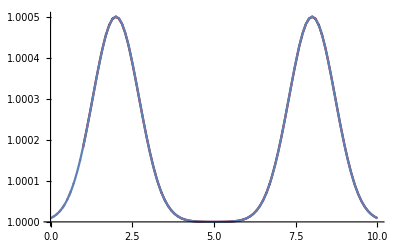

```mathematica
Show[fig2,Plot[rhoAn[x,hy/2,timeP],{x,0,Lx}]]
```

### Center values for graphics

```mathematica
dataAnCenterRhoEqP=ParallelTable[{mmm[[i,1]],rhoAn[mmm[[i,1]],mmm[[i,2]],timeP]+1},{i,mcrCenterLine//Length}];
dataAnCenterU=ParallelTable[{mmm[[i,1]],uAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
dataAnCenterV=ParallelTable[{mmm[[i,1]],vAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
```

```mathematica
dataAnCenterE=Transpose@{dataAnCenterRhoEqP[[All,1]],dataAnCenterRhoEqP[[All,2]]/(γ-1)+1/2 dataAnCenterRhoEqP[[All,2]](dataAnCenterU[[All,2]]*dataAnCenterU[[All,2]] + dataAnCenterV[[All,2]]*dataAnCenterV[[All,2]])};
```

```mathematica
dataAnCenterH=Transpose@{dataAnCenterRhoEqP[[All,1]],1/dataAnCenterRhoEqP[[All,2]](dataAnCenterE[[All,2]] + dataAnCenterRhoEqP[[All,2]])};
```

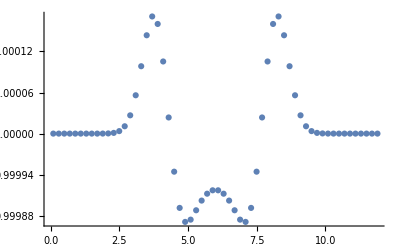

```mathematica
dataExact=ListPlot[dataAnCenterRhoEqP,PlotRange->All]
```

### Error Estimation

```mathematica
cellNodes=Table[{
{MeshCellRcm[[i,1]]-hx/2,MeshCellRcm[[i,2]]-hy/2},
{MeshCellRcm[[i,1]]+hx/2,MeshCellRcm[[i,2]]-hy/2},
{MeshCellRcm[[i,1]]+hx/2,MeshCellRcm[[i,2]]+hy/2},
{MeshCellRcm[[i,1]]-hx/2,MeshCellRcm[[i,2]]+hy/2}},
{i,MeshCellRcm//Length}];
```

```mathematica
cells=Table[Polygon[cellNodes[[i]]],{i,1,cellNodes//Length}];
cells[[1]]
```

Polygon[{{0.,0.},{0.078125,0.},{0.078125,1.},{0.,1.}}]

```mathematica
fDiffer[x_,y_,t_,n_]:=Abs[rhoAn[x,y,t]-GetSol[alpha,n,1,{x,y}]]
```

#### NormC

```mathematica
NMaxValue[{fDiffer[x,y,timeP,1],{x,y}∈cells[[1]]},{x,y}]
```

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.200004

```mathematica
maxitable=ParallelTable[NMaxValue[{fDiffer[x,y,timeP,n],{x,y}∈cells[[n]]},{x,y}],{n,1,cellNodes//Length}];
maxitable[[1]]
```

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

6.43257×10^-8

```mathematica
Max[maxitable]
```

```mathematica
6.5258254733358*^-7
```

```mathematica
1.4483790402586294*^-6 /6.5258254733358*^-7
```

2.21946

#### Norm L1

```mathematica
NIntegrate[fDiffer[x,y,timeP,1],{x,y}∈cells[[1]],
WorkingPrecision->15 ,MaxPoints->2000]
```

1.0819717280141×10^-12

```mathematica
intable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n],{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15 ,MaxPoints->2000],{n,1,cellNodes//Length}];
intable[[1]]
```

1.0819717280141×10^-12

```mathematica
Sum[intable[[i]],{i,intable//Length}]
```

```mathematica
1.84373535687566433811947021850147`15.*^-6
```

```mathematica
1.09375198280445717852985841435017`15.*^-6
```

```mathematica
4.2946188445809258019148826416134`15.*^-7
```

```mathematica
1.39303387530596154344121589865928`15.*^-6
```

```mathematica
1.39680162709597125420651450137597`15.*^-6
```

```mathematica
1.39816238190462637371729712980992`5.*^-6
```

```mathematica
4.4620311025502396 ^-7
```

#### Norm L2

```mathematica
(*надо переделать - квадрат возмущения считают по всей расчетной области*)
```

```mathematica
insqrtable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n]^2,{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15 ,MaxPoints->2000],{n,1,cellNodes//Length}];
insqrtable[[1]]
```

9.42122560599295×10^-24

```mathematica
√Sum[insqrtable[[i]],{i,insqrtable//Length}]
```

```mathematica
8.0061403970885980209334252486821`15.301029995663974*^-7
```

```mathematica
4.4030290576288594175615632742439`15.301029995663981*^-7
```

```mathematica
8.097684201245305212998232964007`15.301029995663962*^-8
```

```mathematica
2.4485155921685051401437828656416`15.301029995663969*^-7
```

```mathematica
8.295058830784622 ^-8
```